```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
```

### specification

This notebook is designed to produce 1000 outputs at three time values (t=1,2,3) for two different models (f1,f2), which depend on three variables (x,y,z) and three parameters (a,b,c) to different degrees.

The idea is that the global sensitivity analysis (in GSA.nb) should be able to identify the most sensitive of these parameters. Using the models and distributions given here, the “correct” result is that model f1 should depend on parameter a most strongly (because of the large range in a), and f2 should depend on variable y most strongly (because of the square term), with some contribution from parameter d (because of the connection with the variable y).

The outputs are saved to an Excel file at the end. GSA.nb is designed to take inputs in the format used here.

```mathematica
SeedRandom[123456789];
```

Define the models:

```mathematica
f1[x_,y_,z_,a_,b_,c_,t_]:=a*x+b*y+c*z*(t-1)+RandomReal[NormalDistribution[0.025,0.00025]]
```

```mathematica
f2[x_,y_,c_,d_,t_]:=c*x*t+d*y^2+RandomReal[NormalDistribution[0.025,0.00025]]
```

Define input ranges:

```mathematica
xdist=UniformDistribution[{94.23398742185837,106.76212063767746}];
ydist=UniformDistribution[{66.04823556312662,134.1721103014048}];
zdist=UniformDistribution[{2061.,2084.}];
adist=UniformDistribution[{-3752.772986238275,27764.96711222388}];
bdist=UniformDistribution[{679.8270214211152,1298.562772661172}];
cdist=UniformDistribution[{164.,198.}];
ddist=UniformDistribution[{164.,198.}];
```

Create tables of inputs:

```mathematica
max=1000;
xtab=Table[RandomReal[xdist],{i,max}];
ytab=Table[RandomReal[ydist],{i,max}];
ztab=Table[RandomReal[zdist],{i,max}];
atab=Table[RandomReal[adist],{i,max}];
btab=Table[RandomReal[bdist],{i,max}];
ctab=Table[RandomReal[cdist],{i,max}];
dtab=Table[RandomReal[ddist],{i,max}];
```

```mathematica
{Min[xtab],Max[xtab]}
{Min[ytab],Max[ytab]}
{Min[ztab],Max[ztab]}
{Min[atab],Max[atab]}
{Min[btab],Max[btab]}
{Min[ctab],Max[ctab]}
{Min[dtab],Max[dtab]}
```

{94.2372,106.664}

{66.0522,134.17}

{2061.,2083.96}

{-3741.94,27725.1}

{681.235,1298.02}

{164.025,197.965}

{164.009,197.952}

Create tables of outputs:

```mathematica
f1tab=Table[Table[f1[xtab[[i]],ytab[[i]],ztab[[i]],atab[[i]],btab[[i]],ctab[[i]],t],{i,max}],{t,1,3,1}];
f2tab=Table[Table[f2[xtab[[i]],ytab[[i]],ctab[[i]],dtab[[i]],t],{i,max}],{t,1,3,1}];
```

Histograms:

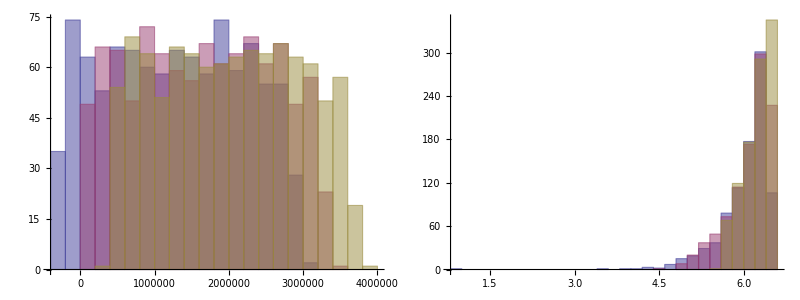

```mathematica
{{Histogram[f1tab,20,ImageSize->400],Histogram[Log[10,f1tab],20,ImageSize->400]}}//TableForm
```

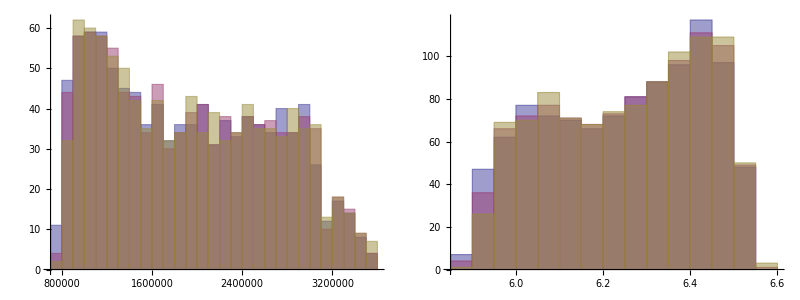

```mathematica
{{Histogram[f2tab,20,ImageSize->400],Histogram[Log[10,f2tab],20,ImageSize->400]}}//TableForm
```

Scatter plots:

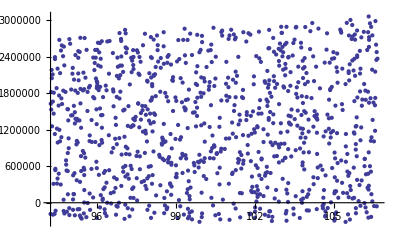
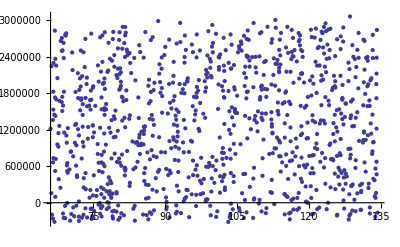
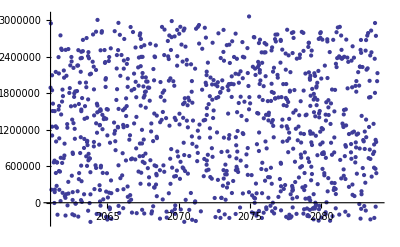
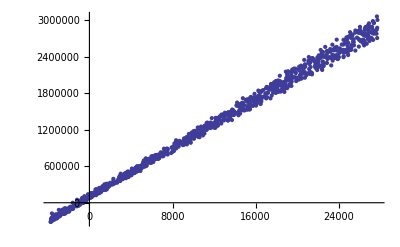
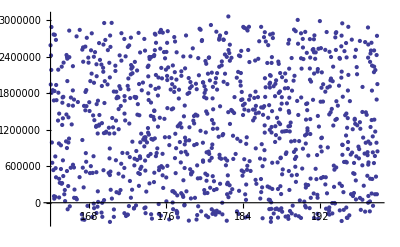
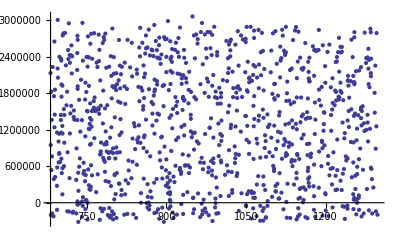
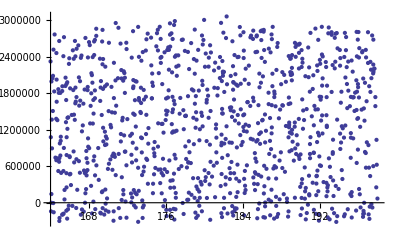
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- -Graphics- | -Graphics-

```mathematica
{{ListPlot[Table[{xtab[[i]],f1tab[[1,i]]},{i,max}],PlotRange->All,ImageSize->400],ListPlot[Table[{ytab[[i]],f1tab[[1,i]]},{i,max}],PlotRange->All,ImageSize->400],ListPlot[Table[{ztab[[i]],f1tab[[1,i]]},{i,max}],PlotRange->All,ImageSize->400],ListPlot[Table[{atab[[i]],f1tab[[1,i]]},{i,max}],PlotRange->All,ImageSize->400],ListPlot[Table[{btab[[i]],f1tab[[1,i]]},{i,max}],PlotRange->All,ImageSize->400]ListPlot[Table[{ctab[[i]],f1tab[[1,i]]},{i,max}],PlotRange->All,ImageSize->400],ListPlot[Table[{dtab[[i]],f1tab[[1,i]]},{i,max}],PlotRange->All,ImageSize->400]}}//TableForm
```

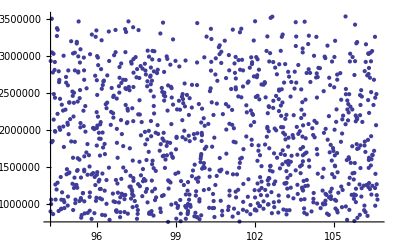
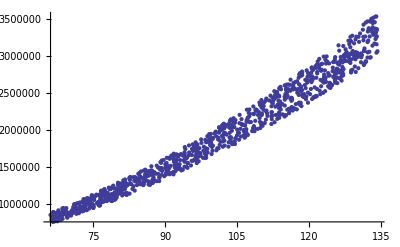
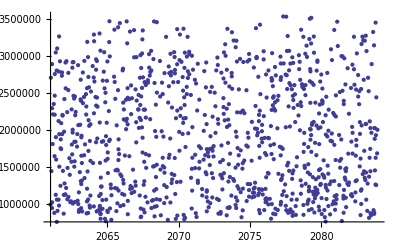
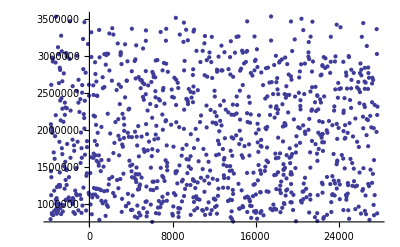
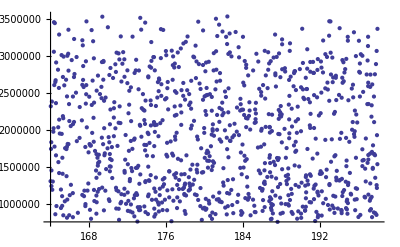
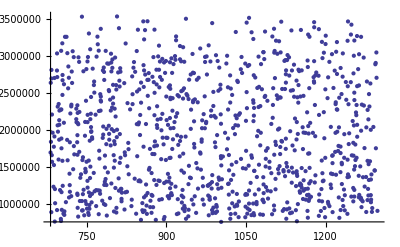
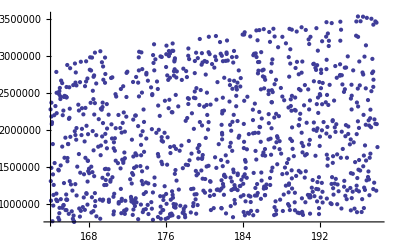
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- -Graphics- | -Graphics-

```mathematica
{{ListPlot[Table[{xtab[[i]],f2tab[[1,i]]},{i,max}],PlotRange->All,ImageSize->400],ListPlot[Table[{ytab[[i]],f2tab[[1,i]]},{i,max}],PlotRange->All,ImageSize->400],ListPlot[Table[{ztab[[i]],f2tab[[1,i]]},{i,max}],PlotRange->All,ImageSize->400],ListPlot[Table[{atab[[i]],f2tab[[1,i]]},{i,max}],PlotRange->All,ImageSize->400],ListPlot[Table[{btab[[i]],f2tab[[1,i]]},{i,max}],PlotRange->All,ImageSize->400]ListPlot[Table[{ctab[[i]],f2tab[[1,i]]},{i,max}],PlotRange->All,ImageSize->400],ListPlot[Table[{dtab[[i]],f2tab[[1,i]]},{i,max}],PlotRange->All,ImageSize->400]}}//TableForm
```

### save data to file

```mathematica
sheet[1]=Table[Table[f1tab[[i,ii]],{i,3}],{ii,max}];
sheet[2]=Table[Table[f2tab[[i,ii]],{i,3}],{ii,max}];
sheet[3]=Table[{xtab[[i]]},{i,max}];
sheet[4]=Table[{ytab[[i]]},{i,max}];
sheet[5]=Table[{ztab[[i]]},{i,max}];
sheet[6]=Table[{atab[[i]]},{i,max}];
sheet[7]=Table[{btab[[i]]},{i,max}];
sheet[8]=Table[{ctab[[i]]},{i,max}];
sheet[9]=Table[{dtab[[i]]},{i,max}];
```

```mathematica
outputs=Table[sheet[i],{i,9}];
```

```mathematica
Length[Flatten[outputs]]
```

13000

```mathematica
headers={"f1","f2","x","y","z","a","b","c","d"}
```

{f1,f2,x,y,z,a,b,c,d}

```mathematica
Export["ExampleData.xls",Table[headers[[i]]->outputs[[i]],{i,9}],"XLS"]
```

ExampleData.xls